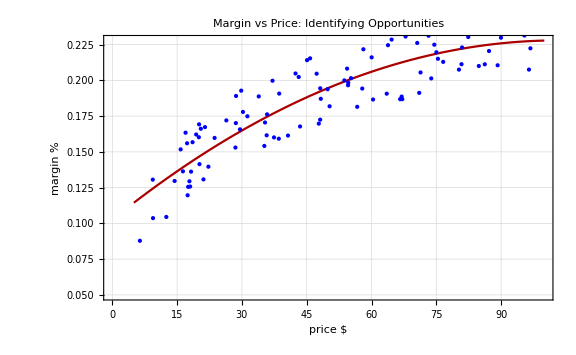

```mathematica
Module[{samples,n=100,margin,data,fit},
samples=RandomReal[{5,100},n];
margin=((Log@#+RandomReal[{-.5,.5}])/20)&/@samples;
data=Transpose[{samples,margin}];
fit=NonlinearModelFit[data,a x^2+b x + c,{a,b,c},x];
Plot[fit[x],{x,5,100},
PlotStyle->Darker@Red,
Epilog->{PointSize@Medium,Blue,Point@data},
Frame->True,FrameStyle->Medium,PlotRange->{Automatic,{.05,Automatic}},AxesOrigin->{0,0},
GridLines->Automatic,
ImageSize->Large,PlotLabel->Style["Margin vs Price: Identifying Opportunities",{Black, Large}],
FrameLabel->(Style[#,{Black,16}]&/@{"price $","margin %"})]]
```